# L0 Gun Modeling

```mathematica
root=NotebookDirectory[]
```

/Users/cem52/accuser/erl/CERL/lattice_devel/CornellBNL/model/in/a1/gun/

```mathematica
scratchdir="~/Desktop/";
```

```mathematica
rawGunFilename="dcgun_GHV_OUTSF7.TXT";
outputFilename = "in.gun_grid.bmad";
outputWallFilename = "in.gun_wall.bmad";

bmadelename = "in.gun";
```

```mathematica
cLightN=299792458.
```

2.99792×10^8

```mathematica
(*rawGunFilename="test_OUTSF7.TXT";
```

## Options

```mathematica
myplotoptions={BaseStyle->{FontSize->15}, Frame->True};
SetOptions[Plot,myplotoptions];
SetOptions[ListPlot,myplotoptions];
SetOptions[ListLogPlot,myplotoptions];
SetOptions[ListVectorPlot,myplotoptions];
SetOptions[ListDensityPlot,myplotoptions];
```

## raw grid data

https://wiki.lepp.cornell.edu/lepp/bin/view/ERL/Private/GunGHVFieldMap
2D field map for Parmela. Rmax is 10 mm, and the increments of R is 0.5 mm. The increments of Z is 0.25 mm. The Gun voltage is -500 kV.

-Graphics-

-Graphics-

```mathematica
rawgriddat=Import[root<>rawGunFilename, "Table", "HeaderLines"->27];
```

```mathematica
rawgriddat[[1;;8]]//Grid
```

Electric | fields | for | a | rectangular | area | with | corners | at:
(Rmin,Zmin) | = | (0.0,-150) |  |  |  |  |  | 
(Rmax,Zmax) | = | (26,0.0) |  |  |  |  |  | 
R | and | Z | increments: | 104 | 600 |  |  | 
 |  |  |  |  |  |  |  | 
R | Z | Er | Ez | |E| | V |  |  | 
(mm) | (mm) | (V/cm) | (V/cm) | (V/cm) | (V) |  |  | 
0. | -150. | 0. | -54802.7 | 54802.7 | -500000. |  |  |

```mathematica
xC=1;
zC=2;
ExC=3;
EzC=4;
griddat={10^-3(*m/mm*)#[[1]], 10^-3(*m/mm*)#[[2]]+0.15, 100(*cm/m*)#[[3]],  100 (*cm/m*)#[[4]]}&/@rawgriddat[[8;;]];
```

-Graphics-

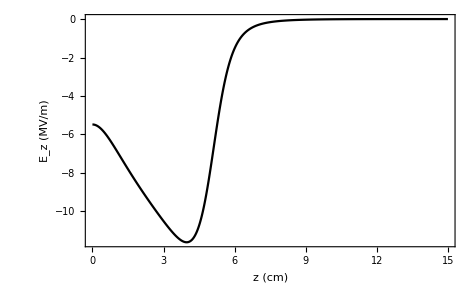

```mathematica
ListPlot[{#⟦xC ⟧, #⟦zC ⟧}&/@griddat, FrameLabel->{"r (m)", "z (m)"}, AspectRatio->Automatic, ImageSize->100]
```

```mathematica
dat0=Select[griddat,# ⟦xC⟧<0.0001&];
dat1=Select[griddat,0.0001<# ⟦xC⟧<0.000251&];Length[dat1]
```

601

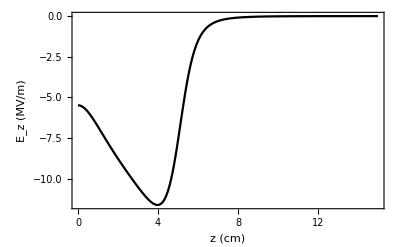

```mathematica
ListPlot[{100 #⟦zC ⟧, 10^-6#⟦EzC⟧}&/@dat0, PlotStyle->Black, Joined->True, FrameLabel->{"z (cm)", "E_z (MV/m)"}]
```

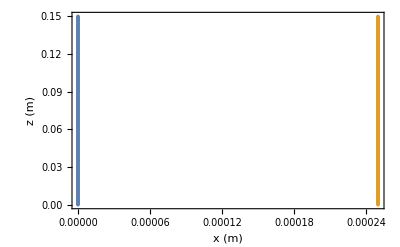

```mathematica
ListPlot[{{#⟦xC ⟧, #⟦zC ⟧}&/@dat0, {#⟦xC ⟧, #⟦zC ⟧}&/@dat1}, FrameLabel->{"x (m)", "z (m)"}]
```

```mathematica
{Min[dat0[[All,xC]]], Max[dat0[[All,xC]]], Min[dat1[[All,xC]]], Max[dat1[[All,xC]]]}
```

{0.,0.,0.00025,0.00025}

```mathematica
{Min[dat0[[All,zC]]], Max[dat0[[All,zC]]]}
```

{0.,0.15}

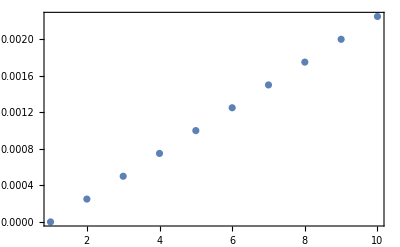

```mathematica
ListPlot[dat0[[1;;10,zC]],PlotRange->All]
```

```mathematica
dat0[[1;;3,zC]]
```

{0.,0.00025,0.0005}

## 1 D vs 3 D

```mathematica
zlist =Union[ griddat⟦All,zC⟧,griddat⟦All,zC⟧];
zmin = Min[zlist ];
zmax = Max[zlist ];
Length[zlist]
```

601

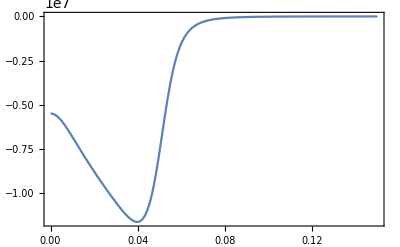

```mathematica
Ez0 = Interpolation[{#⟦zC ⟧,#⟦EzC⟧}&/@dat0];
Plot[Ez0[z], {z,zmin,zmax}]
```

```mathematica
(*Astra field expansion formulas*)
Ez[r_,z_]:=Ez0[z] - r^2/4(Ez0''[z]) ;
Er[r_,z_]:=-r/2 Ez0'[z] + r^3/16(Ez0''[z] )
```

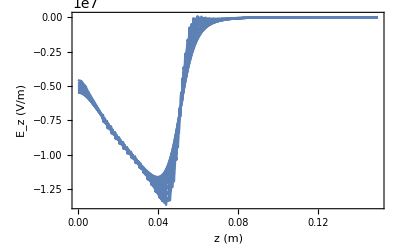

```mathematica
rmin=0;
rmax = 0.01;
dr = 0.001;
Plot[Table[Ez[r, z], {r,rmin,rmax,dr}], {z,zmin,zmax}, FrameLabel->{"z (m)", "E_z (V/m)"}]
```

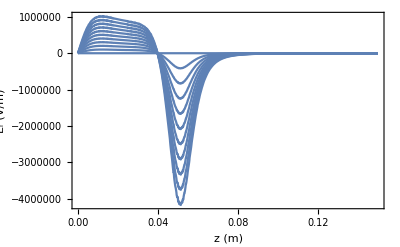

```mathematica
Plot[Table[Er[r, z], {r,rmin,rmax,dr}], {z,zmin,zmax}, FrameLabel->{"z (m)", "E_r (V/m)"}, PlotRange->All]
```

```mathematica
xlist =Union[ griddat⟦All,xC⟧,griddat⟦All,xC⟧];
xmin = Min[xlist ];
xmax = Max[xlist ];
Length[xlist]
```

105

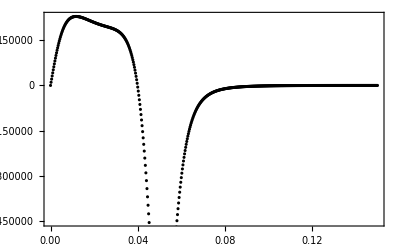

```mathematica
ListPlot[{#⟦zC⟧, #⟦ExC⟧}&/@Select[griddat, #⟦xC⟧==xlist⟦10⟧&], PlotStyle->Black]
```

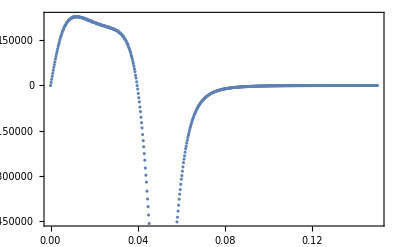

```mathematica
ListPlot[{ #⟦zC⟧, Er[#⟦xC⟧, #⟦zC⟧]}&/@Select[griddat, #⟦xC⟧==xlist⟦10⟧&]]
```

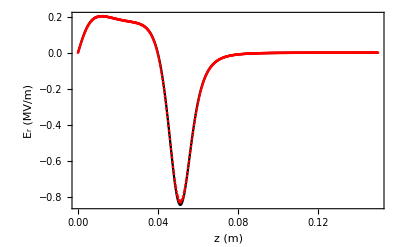

```mathematica
Clear[CompareExAt];
CompareExAt[x_]:=Module[{mydat},
mydat = Select[griddat, #⟦xC⟧==Nearest[xlist,x]⟦1⟧&];
ListPlot[{({#⟦zC⟧, 10^-6#⟦ExC⟧}&/@mydat), ({ #⟦zC⟧, 10^-6 Er[#⟦xC⟧, #⟦zC⟧]}&/@mydat)}, 
 PlotRange->All,
 PlotStyle->{Black, Red}, Joined->{True, False}, FrameLabel->{"z (m)", "E_r (MV/m)", "x = "<>ToString[x]}]
];
CompareExAt[.002]
```

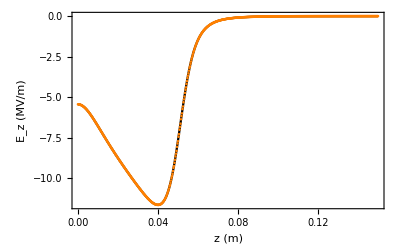

```mathematica
Clear[CompareEzAt];
CompareEzAt[x_]:=Module[{mydat},
mydat = Select[griddat, #⟦xC⟧==Nearest[xlist,x]⟦1⟧&];
ListPlot[{({#⟦zC⟧, 10^-6#⟦EzC⟧}&/@mydat), ({ #⟦zC⟧, 10^-6 Ez[#⟦xC⟧, #⟦zC⟧]}&/@mydat)}, 
 PlotRange->All,
 PlotStyle->{Black, Orange}, Joined->{True, False}, FrameLabel->{"z (m)", "E_z (MV/m)", "x = "<>ToString[x]}]
];
CompareEzAt[.002]
```

```mathematica
(*Export["~/Desktop/test1dfine", Table[{z -.075, Ez0[z]}, {z,0, 0.15, .0001}], "Table"]*)
```

~/Desktop/test1dfine

## Verify Grid

```mathematica
refdat=griddat;
```

```mathematica
xlist=Sort[#[[xC]]&/@refdat, #1<#2&];xlist=Intersection[xlist,xlist];
zlist=Sort[#[[zC]]&/@refdat, #1<#2&];zlist=Intersection[zlist,zlist];
xmax = Max[xlist];xmin = Min[xlist];xsize=xmax-xmin;
zmax = Max[zlist];zmin = Min[zlist];zsize=zmax-zmin;
```

```mathematica
Grid[{{,"min (m)","max (m)"},{"x: ",xmin,xmax}, {"z: ",zmin,zmax}}, Frame->True, Alignment->Left]
```

| min (m) | max (m)
x:  | 0. | 0.026
z:  | 0. | 0.15

```mathematica
Δz = 0.00025;
Δx = 0.00025;
izof[z_]:=Round[(z -zmin)/Δz];
ixof[x_]:=Round[(x -xmin)/Δx];
zof[iz_]:=zmin + iz Δz;
xof[ix_]:=xmin + ix Δx;
```

```mathematica
izof[zmin]
```

0

```mathematica
ixof[xmin]
```

0

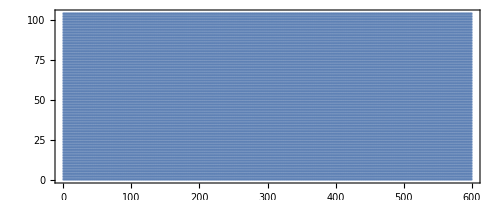

```mathematica
ListPlot[{izof[#[[zC]]],izof[#[[xC]]]}&/@refdat, AspectRatio->Automatic]
```

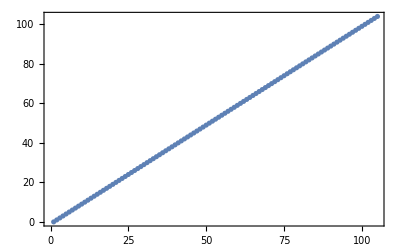

```mathematica
ListPlot[ixof/@xlist]
```

```mathematica
Length[xlist]
```

105

```mathematica
Length[zlist]
```

601

```mathematica
ListPointPlot3D[{{izof[#⟦zC⟧] ,ixof[#⟦xC⟧],10^-6#[[EzC]]}&/@refdat, {izof[#⟦zC⟧] ,ixof[#⟦xC⟧],10^-6#[[ExC]]}&/@refdat}, PlotRange->All, PlotStyle->{{PointSize[Tiny], Blue},{PointSize[Tiny], Red}},AxesLabel->{"x index", "z index", "E (MV/m)"}, BaseStyle->{FontSize->15}]
```

-Graphics3D-

```mathematica
array=Table[0, {Length[xlist]}, {Length[zlist]}];
(array[[ ixof[#⟦xC⟧]+1,izof[#⟦zC⟧] +1]]=#[[EzC]])&/@refdat;
```

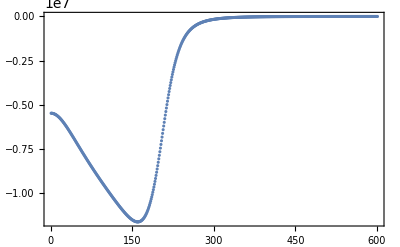

```mathematica
ListPlot[array[[5,All]]]
```

```mathematica
ListDensityPlot[array, DataRange->{{zmin,zmax}, {xmin,xmax}}, PlotRange->All]
```

-Graphics-

## Make Bmad Grid

```mathematica
fieldmapdir = root;

axisdat=Select[refdat, #[[xC]]==0&];
maxEz0=Max[Abs[axisdat[[All,EzC]]]];
iEz0=Interpolation[{#⟦zC⟧,#⟦EzC⟧}&/@axisdat];
maxz=Max[axisdat[[All,zC]]];
voltage = -Integrate[iEz0[z], {z,0,maxz}]
```

499999.

```mathematica
fieldscale=1/voltage;

note={
"! field from file: "<>rawGunFilename,

"! Field scaled for 1 V"};
```

```mathematica
(*pt format: pt(ir, iz) = ( (ErRe,ErIm), (0,0), (EzRe,EzIm), (0,0), (BrRe,BrIm), (0,0), (BϕRe, BϕIm) , (0,0) ) *)
MakeBmadGrid[dat_]:=Module[{header, body, ptlist},
header = {"{ "};
body = {
{"master_parameter = voltage,"},
{"geometry = rotationally_symmetric_rz,"},
{"harmonic = 0,"},
{"field_type = electric,"},
{"r0 = (",xmin,"," ,0 ,")," },
{"dr = (", Δx,",", Δz, "),"}
};

ptlist ={
"pt(", ixof[ #⟦xC⟧  ], "," ,izof[#⟦zC⟧]  ,") = ( ",
	ToString[fieldscale*#⟦ExC⟧, FortranForm],", 0, ",ToString[fieldscale*#⟦EzC⟧, FortranForm]," )", ","}&/@dat;
ptlist[[-1,-1]] = "}";
Join[header,note, body,  ptlist]

]
```

```mathematica
griddata=MakeBmadGrid[refdat ];
```

```mathematica
ExportString[griddata[[1;;10]]~Join~griddata[[-2;;-1]], "Table", "FieldSeparators"->""]
```

{ 
! field from file: dcgun_GHV_OUTSF7.TXT
! Field scaled for 1 V
master_parameter = voltage,
geometry = rotationally_symmetric_rz,
harmonic = 0,
type = electric,
r0 = (0.,0),
dr = (0.00025,0.00025),
pt(0,0) = ( 0., 0, -10.960556590858245 ),
pt(103,600) = ( -0.00024269636736647395, 0, 0. ),
pt(104,600) = ( -0.00023150215042192694, 0, 0. )}

```mathematica
command="mv "<>scratchdir<>outputFilename<>" "<>fieldmapdir <>outputFilename;
Export[NotebookDirectory[]<>outputFilename  ,griddata, "Table", "FieldSeparators"->""];
```

## Boundary

```mathematica
rawbdat=Import[root<>"dcgun_OUTAUT.TXT", "Table"];
```

```mathematica
rawbdat[[1;;68]]
```

{{Los,Alamos,National,Laboratory,Poisson,Superfish},{Program,Automesh,written,by,James,H.,Billen,and,Lloyd,M.,Young},{},{The,original,Poisson,Superfish,codes,were,developed},{by,Ron,F.,Holsinger,in,collaboration,with,Klaus,Halbach.},{These,programs,are,provided,as,a,service,to,the,accelerator},{community,by,the,Los,Alamos,Accelerator,Code,Group,(LAACG).},{},{(c),Copyright,1985-2005,,by,the,Regents,of,the,University,of,California.},{This,software,was,produced,under,U.,S.,Government,contract,W-7405-ENG-36},{by,Los,Alamos,National,Laboratory,,which,is,operated,by,the,University},{of,California,for,the,U.,S.,Department,of,Energy.,Neither,the,Government},{nor,the,University,makes,any,warranty,,express,or,implied,,or,assumes},{any,liability,or,responsibility,for,its,use,,or,represents,that,use,of},{this,software,would,not,infringe,privately,owned,rights.},{Unpublished,-,rights,reserved,under,Copyright,Laws,of,the,United,States.},{},{},{Program,Automesh,7.17,released,1-13-2006},{Program,file:,C:\LANL\AUTOMESH.EXE},{Problem,file:,Z:\USERS\CEM52\DESKTOP\DCGUN\DCGUN.AM,10-08-2012,16:03:00},{SF.INI,file:,C:\LANL\SF.INI,10-08-2012,16:57:12},{},{Problem,description:},{Electrostatic,problem,,Cylindrical,Electrode},{Voltage,=,500000,kV,on,the,inner,conductor},{},{Coordinates,and,lengths,have,dimensions,of,millimeters.},{All,subsequent,programs,require,these,units,for},{entry,of,CON,elements,with,linear,dimensions.},{Note:,Temporary,file,TAPE36,and,the,binary,solution},{file,always,use,dimensions,of,centimeters,for},{the,coordinate,arrays.},{},{Region,data:},{IREG,=,1},{MAT,=,1},{CUR,=,0.},{DEN,=,0.},{ITRI,=,2,[right,triangles]},{IBOUND,=,0,[Dirichlet,boundary]},{IPDIAG,=,0,[no,extra,Automesh,diagnostics]},{DX,=,0.2},{XMIN,=,0.},{XREG(1),=,20},{XREG(2),=,83},{XREG(3),=,88},{XMAX,=,229.02},{DY,=,0.2},{YMIN,=,-236.4},{YMAX,=,0.},{DX1,=,0.2},{KREG(1),=,101},{DXT(2),=,0.398734},{KREG(2),=,259},{DXT(3),=,0.833333},{KREG(3),=,265},{DXT(4),=,1.65906},{KMAX,=,350},{DY1,=,0.2},{LMAX,=,1183},{ITOT,=,417120},{Memory,used,for,the,solution,file:,15.016,M},{Memory,used,for,Automesh,setup,data:,2.511,M},{},{Region,1,boundary,points,from,the,PO,namelist:},{Point,NT,X0,Y0,X,Y,R,THETA,A,B},{1,1,0.,-236.4}}

```mathematica
rawbdat⟦80;;85⟧
```

{{13,4,16.47,-95.92,9.61,9.61},{14,1,26.,-91.48},{15,1,26.,0.},{16,1,0.,0.},{17,1,0.,-236.4},{}}

```mathematica
i1=68;
i2 = 84;
bdat=rawbdat⟦i1;;i2⟧
```

{{1,1,0.,-236.4},{2,1,229.,-236.4},{3,1,229.,-151.7},{4,4,147.2,-69.91,81.79,81.79},{5,1,79.77,-69.91},{6,1,37.57,-69.91},{7,4,29.57,-77.91,8.,8.},{8,1,29.57,-89.77},{9,5,27.46,-94.3,5.,5.},{10,1,17.81,-98.8},{11,5,12.41,-100.,12.79,12.79},{12,5,12.41,-96.83,1.59,1.59},{13,4,16.47,-95.92,9.61,9.61},{14,1,26.,-91.48},{15,1,26.,0.},{16,1,0.,0.},{17,1,0.,-236.4}}

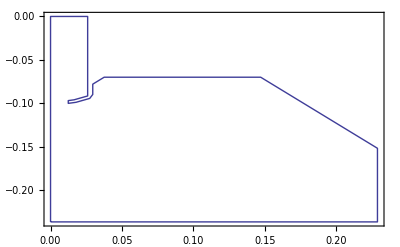

```mathematica
ListPlot[{1/1000#⟦3⟧,1/1000 #⟦4⟧}&/@bdat, Joined->True]
```

```mathematica
sdat={#⟦3⟧, #⟦4⟧}&/@bdat⟦5;;16⟧
```

{{79.77,-69.91},{37.57,-69.91},{29.57,-77.91},{29.57,-89.77},{27.46,-94.3},{17.81,-98.8},{12.41,-100.},{12.41,-96.83},{16.47,-95.92},{26.,-91.48},{26.,0.},{0.,0.}}

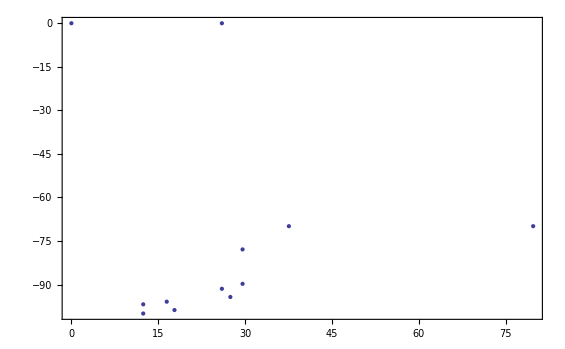

```mathematica
ListPlot[sdat, Joined->False]
```

```mathematica
ProcessPoint[p_]:=Module[{pout, x, y,r},
x=p⟦3⟧;
y= p⟦4⟧;
If[Length[p]==4,pout={{x,y}}];

If[Length[p]==6, 
r= p⟦5⟧;
pout=Table[ {x + r Cos[θ], y + r Sin[θ] -r}, {θ, π/2,3π/2, π/32.0}];
];

pout

]
```

```mathematica
bdat[[12]]
```

{12,5,12.41,-96.83,1.59,1.59}

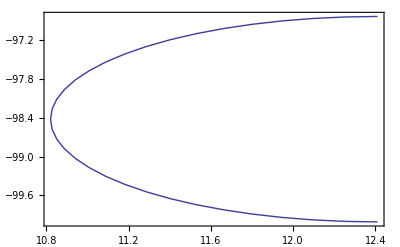

```mathematica
ListPlot[Flatten[ProcessPoint/@bdat⟦12;;12⟧,1], Joined->True]
```

```mathematica
irispoints = Flatten[ProcessPoint/@bdat⟦12;;12⟧, 1];

(*Points found by hand*)
handirispoints={
{26,0},
{26, -91.48},
{23.753, -92.527},
{22.178, -93.262},
{20.035, -94.267},
{18.758, -94.858},
{17.41, -95.486},
{16.217, -96.042},
{15.281, -96.382},
{14.018, -96.687},
{12.84, -96.813}};

handcathodepoints={
{10.82,- 150},
{18.492, -146.64},
{23.915, -144.11},
{28.811, -141.78},
{34.919, -139.05},
{39.71, -137.59},
{47.555, -136.66}


};

(*fake boundary in the gap, becaues Bmad can't do 'reentrant' shapes*)
handgappoints={
{47.555, Last[irispoints]⟦2⟧ - 1.0}
};
boundarypoints = Join[irispoints,handirispoints, handcathodepoints, handgappoints];

(*scaled and shifted points*)
boundarypointsZR ={ 0.001(#⟦2⟧ + 150),0.001 #⟦1⟧}&/@boundarypoints;
boundarypointsZR =Sort[boundarypointsZR , #1⟦1⟧<#2⟦1⟧&];
```

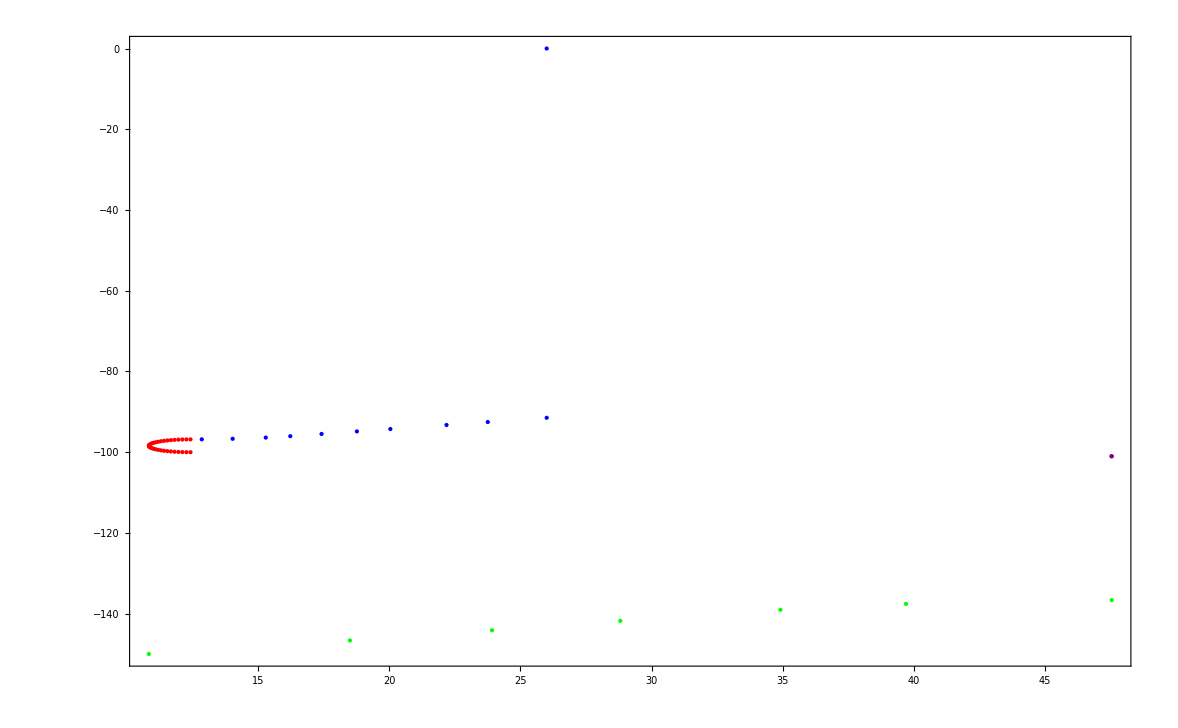

```mathematica
ListPlot[{irispoints,handirispoints, handcathodepoints, handgappoints}, PlotStyle->{Red,Blue,Green, Purple},PlotRange->All]
```

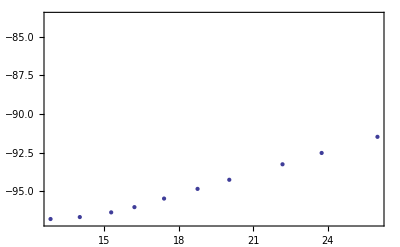

```mathematica
ListPlot[handirispoints]
```

### Wall file

```mathematica
sectionheader={{bmadelename<>"[wall] = {"}};
sectionlist={"section = { s = ", #⟦1⟧, ", v(1) = {0.0, 0.0, " , #⟦2⟧, "} }," }&/@boundarypointsZR ;
sectionlist[[-1,-1]] = "}}}";
```

```mathematica
(sectionheader~Join~sectionlist)[[1;;10]]
```

{{in.gun[wall] = {},{section = { s = ,0.,, v(1) = {0.0, 0.0, ,0.01082,} },},{section = { s = ,0.00336,, v(1) = {0.0, 0.0, ,0.018492,} },},{section = { s = ,0.00589,, v(1) = {0.0, 0.0, ,0.023915,} },},{section = { s = ,0.00822,, v(1) = {0.0, 0.0, ,0.028811,} },},{section = { s = ,0.01095,, v(1) = {0.0, 0.0, ,0.034919,} },},{section = { s = ,0.01241,, v(1) = {0.0, 0.0, ,0.03971,} },},{section = { s = ,0.01334,, v(1) = {0.0, 0.0, ,0.047555,} },},{section = { s = ,0.04899,, v(1) = {0.0, 0.0, ,0.047555,} },},{section = { s = ,0.04999,, v(1) = {0.0, 0.0, ,0.01241,} },}}

```mathematica
command = "mv "<>scratchdir<>outputWallFilename<>" "<>root<>outputWallFilename;
Export[scratchdir<>outputWallFilename  ,sectionheader~Join~sectionlist, "Table", "FieldSeparators"->""];
Run[command]
```

0

```mathematica
(*Simple text file*)
header={{"z(m)", "radius(m)"}};
Export[root<>bmadelename<>"_wall.txt", Join[header, boundarypointsZR], "Table"]
```

/Volumes/user/cem52/erl/CERL/lattice_devel/Phase1B/model/a1/gun/in.gun_wall.txt

## EM Field query

```mathematica
fieldquerydir=root;
```

```mathematica
it = 1;
ix = 2;
iy =3;
is = 4;
iEx=5;
iEy=6;
iEs=7;
iBx=8;
iBy=9;
iBs=10;
```

### Field on axis

```mathematica
selebeg=0;

smin =0+selebeg;
smax = 0.15+selebeg
myt=0;
myx=0.0;
myy=0.0;
sampledat=Table[{myt, myx, myy, s}, {s, smin, smax, (smax-smin)/100}];
Export[fieldquerydir<>"querypoints.dat",Join[{{Length[sampledat]}}, sampledat],  "Table"]
```

0.15

/Volumes/user/cem52/linux_lib/experimental/bmad_to_opal/test/injector_gun/querypoints.dat

```mathematica
dat=Import[fieldquerydir<>"querypoints.out",  "Table"][[2;;]];
```

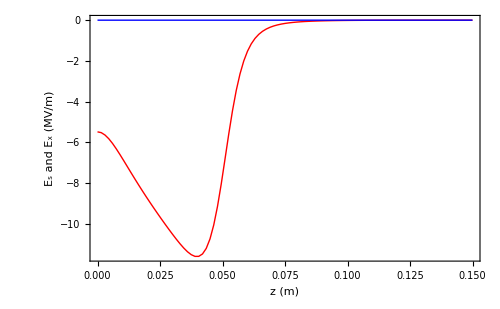

```mathematica
g1=ListPlot[{#[[is]], 10^-6 #[[iEs]]}&/@dat, Joined->True,PlotRange->All, Frame->True, BaseStyle->{FontSize->15}, FrameLabel->{"s (m)", "E_s (MV/m)"}, PlotStyle->Red];
g2=ListPlot[{#[[is]], 10^-6#[[iEx]]}&/@dat, Joined->True,PlotRange->All, Frame->True, BaseStyle->{FontSize->15}, FrameLabel->{"s (m)", "E_x (MV/m)"}, PlotStyle->Blue];
Show[g1,g2, PlotRange->All, FrameLabel->{"z (m)", "E_s and E_x (MV/m)"}, ImageSize->500]
```

### Field on a flat grid

```mathematica
selebeg=0;

smin =0+selebeg;
smax = 0.15+selebeg;
myy=0;
myt=0;
xmax = 0.01;
nx=40;
ns=200;
xstep=(xmax-xmin)/(nx-1);
 sstep=(smax-smin)/(ns-1);

isof[s_]:=Round[(s-smin)/sstep];
ixof[x_]:=Round[(x -xmin)/xstep];
zof[is_]:=smin + is sstep;
xof[ix_]:=xmin + ix xstep;

sampledat=Flatten[Table[{myt, x, myy, s}, {x,xmin,xmax,xstep},{s, smin, smax,sstep}], 1];Length[sampledat]
```

8000

```mathematica
Export[root<>"querypoints.dat",Join[{{Length[sampledat]}}, sampledat],  "Table"]
```

/Volumes/user/cem52/erl/CERL/lattice_devel/model/in_grid/L0_gun/querypoints.dat

```mathematica
dat=Import[root<>"querypoints.out",  "Table"][[2;;]];Length[dat]
```

8000

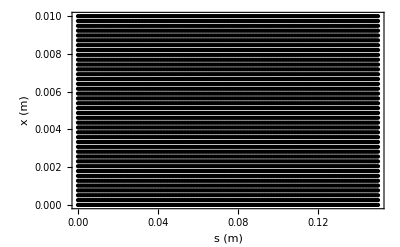

```mathematica
ListPlot[ {#[[is]], #[[ix]]}&/@dat, Frame->True, FrameLabel->{"s (m)", "x (m)"}, BaseStyle->{FontSize->15}, PlotStyle->Black]
```

```mathematica
ListPointPlot3D[{{#⟦is⟧, #⟦ix⟧, #⟦iEs⟧}&/@dat, {#⟦is⟧, #⟦ix⟧, #⟦iEx⟧}&/@dat} , PlotRange->All, PlotStyle->{{PointSize[Tiny], Blue},{PointSize[Tiny], Red}}]
```

-Graphics3D-

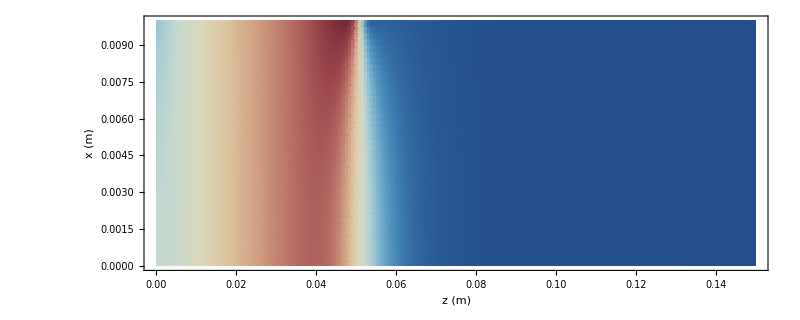

```mathematica
samplegridvalues=Table[0, {ns}, {nx}];
samplegridvalues⟦ isof[#⟦is⟧ ]+1, ixof[ #⟦ix⟧ ] +1⟧ =#⟦iEs⟧;&/@dat;
Show[ListDensityPlot[Transpose[samplegridvalues], DataRange->{{smin,smax}, {xmin,xmax}}, AspectRatio->Automatic, PlotRange->{{smin,smax}, {xmin,xmax}}, ColorFunction->"RedBlueTones", FrameLabel->{"z (m)", "x (m)"}],ImageSize->800]
```

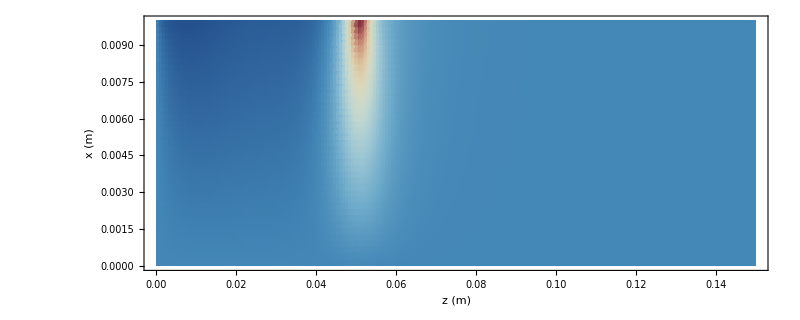

```mathematica
samplegridvalues=Table[0, {ns}, {nx}];
samplegridvalues⟦ isof[#⟦is⟧ ]+1, ixof[ #⟦ix⟧ ] +1⟧ =#⟦iEx⟧;&/@dat;
Show[ListDensityPlot[Transpose[samplegridvalues], DataRange->{{smin,smax}, {xmin,xmax}}, AspectRatio->Automatic, PlotRange->{{smin,smax}, {xmin,xmax},All}, ColorFunction->"RedBlueTones",FrameLabel->{"z (m)", "x (m)"}, PlotRange->All],ImageSize->800]
```

```mathematica
scale=1;
vdat={ {#[[is]], #[[ix]]}, {#[[iBs]],#⟦iBx⟧} } &/@ dat;Length[vdat]
```

10000

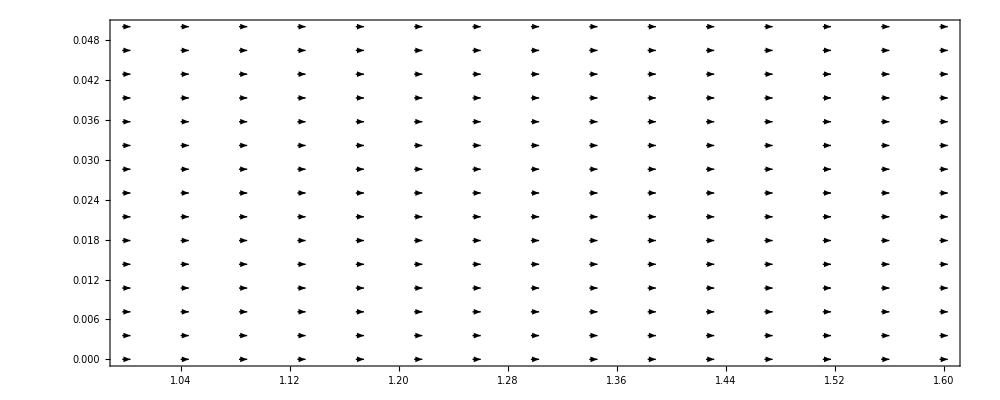

```mathematica
g2=ListVectorPlot[vdat, AspectRatio->Automatic, PlotRange->{{smin,smax},{xmin,xmax}},VectorScale->0.01,VectorPoints->Automatic,VectorStyle->{Black}, ImageSize->1000]
```

```mathematica
Show[g1,g2, FrameLabel->{"s (m)", "x (m)"}]
```

```mathematica
vdat3d={ {xmax/smax#[[4]], #[[2]], #[[3]]},{#[[7]],xmax/smax#[[5]],xmax/smax#[[6]]}} &/@ dat;Length[vdat3d]
```

```mathematica
vdat3d={ {#[[4]], #[[2]], #[[3]]},{0,0,0}} &/@ dat;Length[vdat3d]
```

```mathematica
vdat3d//StandardForm
```

```mathematica
ListVectorPlot3D[vdat3d]
```

```mathematica
ListPlot3D[{ {#[[4]], #[[2]], #[[3]]},{0,0,0}} &/@ dat]
```